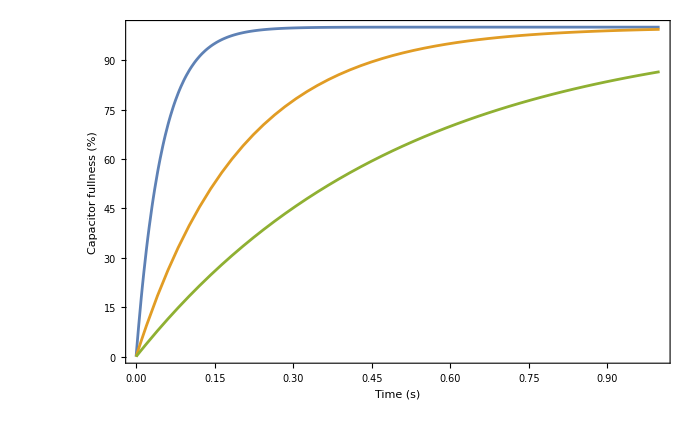

```mathematica
f[R_,CC_,t_]:= 100*(1-Exp[-t/(R*CC)])
Plot[{f[500,100 10^-6,t],f[2000,100 10^-6,t],f[5000,100 10^-6,t]},{t,0,1},PlotRange->All,Frame->True,LabelStyle->{"FontSize" -> 22},FrameLabel->{"Time (s)","Capacitor fullness (%)"}]
```

```mathematica
f[R_,CC_,Start_,End_,t_]:= If[t > Start && t < End,100*(1-Exp[-(t-Start)/(R*CC)]),If[t>=End && t <= 1+End,0.0]]
```

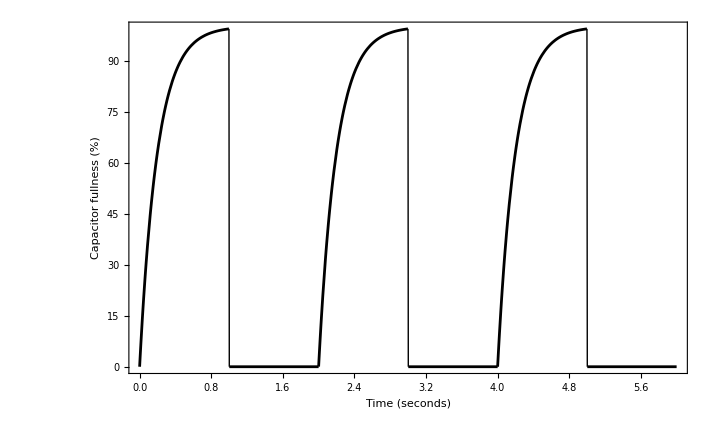

```mathematica
Plot[{f[2000,100 10^-6,0,1,t],f[2000,100 10^-6,2,3,t],f[2000,100 10^-6,4,5,t]},{t,0,6},PlotStyle->Black,Frame->True,FrameLabel->{"Time (seconds)","Capacitor fullness (%)"},LabelStyle->{"FontSize" -> 22},ExclusionsStyle->"Line"]
```